```mathematica
(* Mathematica*)
```

```mathematica
Clear[f,g,h,k,kk,hh,ll,ff,gg,mm]
```

```mathematica
(* cartoons*)
```

```mathematica
f[t_]=Cos[t]
```

Cos[t]

```mathematica
g[t_]=(2+Exp[1-Sin[t]]/Exp[2]-1.3/2)/Sqrt[5.5]
```

0.426401 (1.35+ⅇ^(-1-Sin[t]))

```mathematica
ff[x_]=f[x*2*Pi]
```

Cos[2 π x]

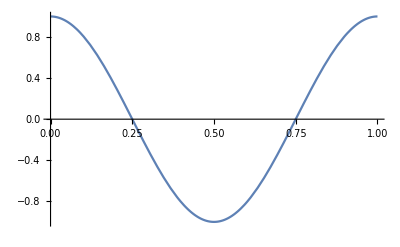

```mathematica
Plot[f[t*2*Pi],{t,0,1}]
```

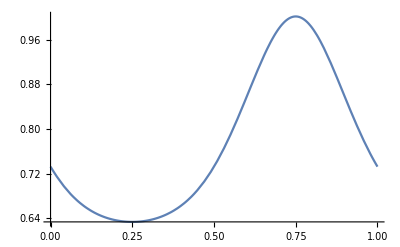

```mathematica
Plot[g[t*2*Pi],{t,0,1}]
```

```mathematica
gg[x_]=g[x*2*Pi]
```

0.426401 (1.35+ⅇ^(-1-Sin[2 π x]))

```mathematica
s0=N[Log[2]/Log[3]]
```

0.63093

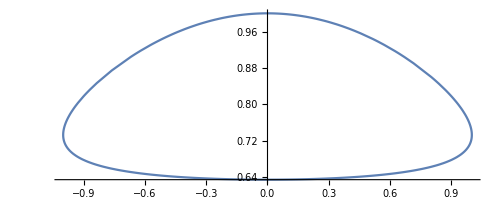

```mathematica
ParametricPlot[{ff[t],gg[t]},{t,0,1}]
```

```mathematica
(*Phased  Mandelbrot Cartoon Function*)
```

```mathematica
kk[x_]=N[Sum[ff[3^k*x]/3^(s0*k),{k,0,20}]];
```

```mathematica
ll[x_]=N[Sum[gg[3^k*(x)]/3^(s0*k),{k,0,20}]];
```

```mathematica
mm[x_]=N[Sum[ff[3^k*(x-1/4)]/3^(s0*k),{k,0,20}]];
```

```mathematica
nn[x_]=N[Sum[ff[3^k*(x+1/4)]/3^(s0*k),{k,0,20}]];
```

```mathematica
a=ParallelTable[{kk[x],ll[x]},{x,0,1,1/100000}];
```

```mathematica
g1=ListPlot[a,ColorFunction->Hue,PlotStyle->PointSize[0.001],ImageSize->2000];
```

```mathematica
aa=ParallelTable[{kk[x],ll[x],mm[x]},{x,0,1,1/375000}];
```

```mathematica
bb=ParallelTable[{kk[x],ll[x],nn[x]},{x,0,1,1/375000}];
```

```mathematica
cc=Join[aa,bb];
```

```mathematica
ga=ListPointPlot3D[cc,ColorFunction->"Rainbow",ImageSize->{2000,2000},PlotStyle->PointSize[0.001]];
```

```mathematica
Export["biscuit_Cartoon_Sinoid_function_Double.jpg",{g1,ga}]
```

biscuit_Cartoon_Sinoid_function_Double.jpg

```mathematica
g2=Show[ga,ViewPoint->{2,2,2},ImageSize->{2000,2000}];
```

```mathematica
Export["Biscuit_Siniod_function_double_g2.jpg" ,g2]
```

Biscuit_Siniod_function_double_g2.jpg

```mathematica
g3=Show[ga,PlotRange->All,ViewPoint->Right,ImageSize->{2000,2000}];
```

```mathematica
Export["Biscuit_Siniod_function_double_g3.jpg" ,g3]
```

Biscuit_Siniod_function_double_g3.jpg

```mathematica
g4=Show[ga,PlotRange->All,ViewPoint->Above,ImageSize->{2000,2000}];
```

```mathematica
Export["Biscuit_Siniod_function_double_g4.jpg" ,g4]
```

Biscuit_Siniod_function_double_g4.jpg

```mathematica
Export["Biscuit_Siniod_function_double_grid.jpg" ,GraphicsGrid[{{ga,g2},{g3,g4}},ImageSize->{4000,4000}]]
```

```mathematica
(*end*)
```